```mathematica
?DSolve
```

DSolve[eqn,y,x] solves a differential equation for the function y, with independent variable x. 
DSolve[{eqn_1,eqn_2,…},{y_1,y_2,…},x] solves a list of differential equations. 
DSolve[eqn,y,{x_1,x_2,…}] solves a partial differential equation.

```mathematica
(*Solve the differential eq d^2x/dt^2=-kx*)
deq=x''[t]+k*x[t]==0;
sol=DSolve[deq,x[t],t]
```

{{x[t]→C[1] Cos[√k t]+C[2] Sin[√k t]}}

```mathematica
xt=x[t]/.sol[[1]]
```

C[1] Cos[√k t]+C[2] Sin[√k t]

```mathematica
vt=D[xt,t]
```

√k C[2] Cos[√k t]-√k C[1] Sin[√k t]

```mathematica
xt=xt/.k->1
vt=vt/.k->1
```

C[1] Cos[t]+C[2] Sin[t]

C[2] Cos[t]-C[1] Sin[t]

```mathematica
eq1=(xt/.t->0)==5
eq2=(vt/.t->0)==1
```

C[1]==5

C[2]==1

```mathematica
constant=Solve[{eq1,eq2},{C[1],C[2]}]
```

{{C[1]→5,C[2]→1}}

```mathematica
xt=xt/.constant[[1]]
vt=vt/.constant[[1]]
```

5 Cos[t]+Sin[t]

Cos[t]-5 Sin[t]

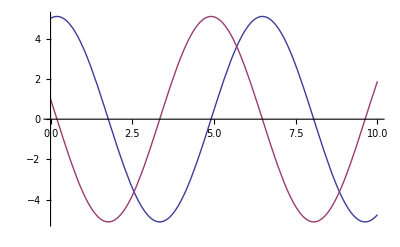

```mathematica
Plot[{xt,vt},{t,0,10}]
```